```mathematica
Animate[
ParametricPlot3D[
{{u,v,√(u^2+v^2-t)},{u,v,-√(u^2+v^2-t)}},
{u,-3,3},
{v,-3,3},
Boxed->False,
Axes->True,
PlotRange->All,
PlotPoints->100
],
{t,-4,4},
AnimationRunning->False,
AnimationRepetitions->1,
AnimationRate->.5,
RefreshRate->2
]
```

```mathematica
Show[
ParametricPlot3D[
{{u,v,√(u^2+v^2-1)}},
{u,-3,3},
{v,-3,3},
Boxed->False,
Axes->True,
PlotPoints->20
],
Graphics3D[{PointSize[Large],Point[{0,√2,1}],Blue,Thick,Arrow[{{0,√2,1},{0,√2+1,1+√2}}]}],
ParametricPlot3D[{t √(1-((√(t^2-1)+1)^2)/(2 t^2)),(√(t^2-1)+1)/(√2),√(t^2-1)},{t,-3,3},PlotStyle->{Red,Thick}],
ParametricPlot3D[{-√2 β,α+√2,√2 α+1},{α,-2,2},{β,-2,2},Mesh->None,PlotStyle->{Green,Opacity[0.5]}],
ParametricPlot3D[{(),√2+t,√(1+2 √2 t+t^2)},{t,-1,3},PlotStyle->{RGBColor[44,216,210],Thick}]
]
```

-Graphics3D-

```mathematica
{ParametricPlot3D[
{{u,v,√(u^2+v^2-1)}},
{u,-3,3},
{v,-3,3},
Boxed->False,
Axes->True,
PlotPoints->20
],
ParametricPlot3D[
{{Cos[u]Cosh[v],Sin[u]Cosh[v],Sinh[v]}},
{u,0,2π},
{v,-3,3},
Boxed->False,
Axes->True,
PlotPoints->20
],
ParametricPlot3D[
{{u Cos[v],u Sin[v],√(u^2-1)}},
{u,0,5},
{v,0,2π},
Boxed->False,
Axes->True,
PlotPoints->20
]
}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
{ParametricPlot3D[
{{Cos[ϕ]+α Sin[ϕ],Sin[ϕ]-α Cos[ϕ],α}},
{ϕ,0,2π},
{α,-5,5},
Boxed->False,
Axes->True,
PlotPoints->20
],
ParametricPlot3D[
{{Cos[ϕ]-α Sin[ϕ],Sin[ϕ]+α Cos[ϕ],α}},
{ϕ,0,2π},
{α,-5,5},
Boxed->False,
Axes->True,
PlotPoints->20
]
}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
Animate[
Show[
ParametricPlot3D[
{{Cos[u]Cosh[v],Sin[u]Cosh[v],Sinh[v]}},
{u,0,2π},
{v,-3,3},
Boxed->False,
Axes->True,
PlotPoints->20
],
ParametricPlot3D[{Cos[u]+u Sin[u], Sin[u]-u Cos[u],u},{u,0,10},PlotStyle->{Dashed,Red}],
Graphics3D[{Black,PointSize[Large],Point[{{Cos[t]+t Sin[t], Sin[t]-t Cos[t],t}}]}],
ParametricPlot3D[{Cos[t]+u Sin[t], Sin[t]-u Cos[t],u},{u,0,10}]
],
{t,0,10},
AnimationRunning->False,
AnimationRepetitions->1,
AnimationRate->.5
]
```

```mathematica
Manipulate[ParametricPlot3D[
{4Cos[θ]+2Cos[θ]Cos[ϕ],4(b+2+2Cos[ϕ])/(4+2Cos[ϕ])Sin[θ]+2(b+2+2Cos[ϕ])/(4+2Cos[ϕ])Sin[θ]Cos[ϕ],2Sin[ϕ]},
{ϕ,0,2π},
{θ,0,2π},
Boxed->False,
Axes->True,
PlotPoints->20
],
{b,0,6}
]
```

```mathematica
Norma[x_]:=√(x.x);
Integrate[
4*Norma[{Cos[u]Cos[v](2+Cos[u]),Cos[u]Sin[v](2+Cos[u]),Sin[u](2+Sin[u](Cos[v])^2+Cos[u](Sin[v])^2)}],{u,0,2π},{v,0,2π}]
```

4 ∫_0^(2 π) ∫_0^(2 π) √(Cos[u]^2 (2+Cos[u])^2 Cos[v]^2+Cos[u]^2 (2+Cos[u])^2 Sin[v]^2+Sin[u]^2 (2+Cos[v]^2 Sin[u]+Cos[u] Sin[v]^2)^2)ⅆvⅆu

```mathematica
N[32 π^2]
```

315.827

```mathematica
S[ϕ_,θ_]:={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],Sin[θ]};
Manipulate[
Show[
ParametricPlot3D[
S[ϕ,θ],
{ϕ,0,2π},
{θ,-π/2,π/2},
Boxed->False,
Axes->False,
PlotPoints->20
],
(*ParametricPlot3D[S[(√(1-ψ^2))/(2ψ)(Log[1-Sin[t]]-Log[1+Sin[t]])+C,t],{t,0,2π},PlotStyle->{Red,Thick}],
ParametricPlot3D[S[-(√(1-ψ^2))/(2ψ)(Log[1-Sin[t]]-Log[1+Sin[t]])+C,t],{t,0,2π},PlotStyle->{Blue,Thick}],*)
ParametricPlot3D[S[(√(1-ψ^2))/(2ψ)(Log[Tan[π/4-t/2]])+C,t],{t,0,2π},PlotStyle->{Green,Thick}],
ParametricPlot3D[S[-(√(1-ψ^2))/(2ψ)(Log[Tan[π/4-t/2]])+C,t],{t,0,2π},PlotStyle->{Orange,Thick}]
],{ψ,-1,1},{C,-2,2}
]
```

```mathematica
Show[
ParametricPlot3D[
{-(4u)/(4+u^2+v^2),-(4v)/(4+u^2+v^2),(2 u^2+2 v^2)/(4+u^2+v^2)},{u,-2,2},{v,-2,2},
Boxed->True,
Axes->True,
PlotPoints->50
]
]
```

-Graphics3D-

```mathematica
Helikoid[u_,v_]:={Sinh[u]Cos[v],Sinh[u]Sin[v],v};
```

```mathematica
Manipulate[
Show[
ParametricPlot3D[
Helikoid[u,v],{u,0,3},{v,-2π,2π},
Boxed->True,
Axes->True,
PlotPoints->30
],
ParametricPlot3D[Helikoid[t,t+C1],{t,0,2π},PlotStyle->Red],ParametricPlot3D[Helikoid[-t,t+C2],{t,-2π,0},PlotStyle->Red],
ParametricPlot3D[Helikoid[ArcSinh[r],t],{t,-2π,2π},PlotStyle->{Blue}]
],{C1,-2π,2π},{C2,-2π,2π},{r,0,Sinh[3]}
]
```

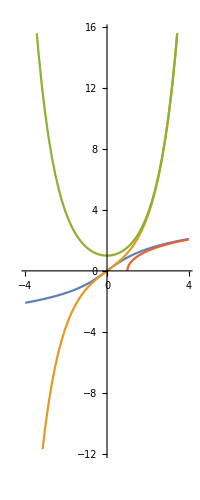

```mathematica
Plot[{ArcSinh[x],Sinh[x],Cosh[x],ArcCosh[x]},{x,-4,4},AxesStyle->Dashed,AspectRatio->Automatic]
```

```mathematica
ParametricPlot3D[{r Cos[ϕ],r Sin[ϕ],r^2},{r,0,3},{ϕ,0,2π},BoxRatios->Automatic,PlotStyle->Directive[Specularity[White,50],Orange],Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
{{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}}.{{Sin[θ],0,Cos[θ]},{0,1,0},{-Cos[θ],0,Sin[θ]}}.{{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}
```

{{Cos[α] Cos[ϕ] Sin[θ]-Sin[α] Sin[ϕ],-Cos[ϕ] Sin[α]-Cos[α] Sin[θ] Sin[ϕ],Cos[α] Cos[θ]},{Cos[ϕ] Sin[α] Sin[θ]+Cos[α] Sin[ϕ],Cos[α] Cos[ϕ]-Sin[α] Sin[θ] Sin[ϕ],Cos[θ] Sin[α]},{-Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],Sin[θ]}}

```mathematica
n[ϕ_,θ_]:={Cos[ϕ]Cos[θ],Sin[ϕ]Cos[θ],Sin[θ]};
M[ϕ_,θ_,α_]:=Inverse[{{Sin[θ],0,Cos[θ]},{0,1,0},{-Cos[θ],0,Sin[θ]}}].Inverse[{{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}}].{{Cos[α],-Sin[α],0},{Sin[α],Cos[α],0},{0,0,1}}.{{Sin[θ],0,Cos[θ]},{0,1,0},{-Cos[θ],0,Sin[θ]}}.{{Cos[ϕ],-Sin[ϕ],0},{Sin[ϕ],Cos[ϕ],0},{0,0,1}};
Manipulate[
Show[
Graphics3D[{Black,PointSize[Large],Point[{a1,a2,a3}Cos[α]+(n[ϕ,θ]×{a1,a2,a3})Sin[α]+n[ϕ,θ](n[ϕ,θ].{a1,a2,a3})(1-Cos[α])],Red,Arrow[{{0,0,0},n[ϕ,θ]}],
Opacity[0.3],InfinitePlane[{0,0,0},{{1,0,0}×n[ϕ,θ],({1,0,0}×n[ϕ,θ])×n[ϕ,θ]}]
},Axes->True,BoxRatios->Automatic,AxesLabel->{x,y,z},PlotRange->{{-3,3},{-3,3},{-3,3}}]
],
{{a1,0},-3,3},{{a2,0},-3,3},{{a3,1},-3,3},
{ϕ,0,2π},{{θ,π/2},-π/2,π/2},{α,0,2π}
]
```

```mathematica
ContourPlot3D[x^4+y^4+z^4-x^2-y^2-z^2+0.5==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->None,PlotPoints->35,ContourStyle->Directive[Specularity[White,50],Orange],Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Manipulate[
ContourPlot3D[x^2/a^2+y^2/b^2-z^2/c^2==T,{x,-2,2},{y,-2,2},{z,-2,2},ContourStyle->Directive[Specularity[White,50],Orange],Lighting->"Neutral"]
,{a,1,4},{b,1,4},{c,1,4},{T,-3,3}]
```

```mathematica
Manipulate[ParametricPlot3D[{u ,v,u^3-3u v^2},{u,-3,3},{v,-3,3},PlotRange->{{-2,2},{-2,2},{-5,5}}]
,{a,1,3},{b,1,3}]
```

```mathematica
Katenoid[φ_,t_]:={Cos[φ]Cosh[t],Sin[φ]Cosh[t],t};
Manipulate[
Show[
ParametricPlot3D[{Cos[φ]Cosh[t],Sin[φ]Cosh[t],t},{φ,0,2π},{t,-2,2},PlotRange->All,PlotStyle->Directive[Specularity[White,50],Orange],Lighting->"Neutral",Boxed->False,Axes->False],
ParametricPlot3D[Katenoid[t,Tan[ψ]t],{t,-2/Tan[ψ],2/Tan[ψ]}]],
{ψ,0,π}]
```

```mathematica
ParametricPlot3D[{{1,1,1}+{1,1,1}*t,{1,1,1}+{1,1,1}*t^3,{1,1,1}+{1,1,1}*Log[t]},{t,0,5}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[a^t,{t,-3,3},PlotRange->{{-3,3}}],{a,0.01,2}]
```

```mathematica
Manipulate[Animate[
Show[
ParametricPlot[{R(t+Cos[-t+π/2]),R (1+Sin[-t+π/2])},{t,0,4π},PlotRange->{{0,4π*R}}],
ParametricPlot[{R(θ+Cos[φ]),R(1+ Sin[φ])},{φ,0,2π}],
Graphics[{PointSize[Large],Point[{R(θ+Cos[-θ+π/2]),R(1+ Sin[-θ+π/2])}],Arrow[{{R θ,R},{R(θ+Cos[-θ+π/2]),R(1+Sin[-θ+π/2])}}]}]
],
{θ,0,4π},AnimationRunning->False,AnimationRate->.2,AnimationRepetitions->1],
{R,1,2}
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{s1+Norm[{m1,m2}-{s1,s2}]Cos[t],s2+Norm[{m1,m2}-{s1,s2}]Sin[t]},{t,0,2π},PlotStyle->Red],
Graphics[{ Blue,PointSize[Large],Point[{Cos[φ](m1-s1)-Sin[φ](m2-s2)+s1,Sin[φ](m1-s1)+Cos[φ](m2-s2)+s2}],Black,PointSize[Large],Point[{s1,s2}]}]
],
{m1,0,3},{m2,0,3},{s1,-2,2},{s2,-2,2},{φ,0,2π}
]
```

```mathematica
Manipulate[
Animate[
Show[
ParametricPlot[{
{R Cos[t],R Sin[t]},
{Cos[θ](R+r-r Cos[t])-r Sin[θ]Sin[t],Sin[θ](R+r-r Cos[t])+r Cos[θ]Sin[t]},
{Cos[t](R+r-m Cos[(R t)/r])+m Sin[t]Sin[(R t)/r],Sin[t](R+r-m Cos[(R t)/r])-m Cos[t]Sin[(R t)/r]}
},{t,0,2π}],
Graphics[{PointSize[Large],Point[{Cos[θ](R+r-m Cos[(R θ)/r])+m Sin[θ]Sin[(R θ)/r],Sin[θ](R+r-m Cos[(R θ)/r])-m Cos[θ]Sin[(R θ)/r]}]}]
],{θ,0,2π},AnimationRunning->False,AnimationRate->.1,AnimationRepetitions->1]
,{R,0.1,3},{r,0.1,3},{{m,r},0.1,r+R}]
```

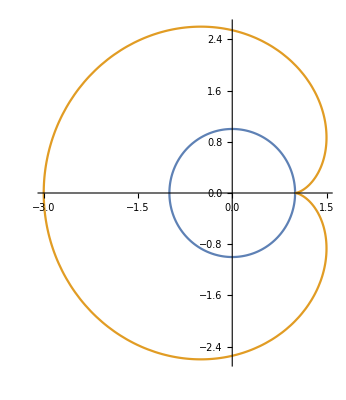
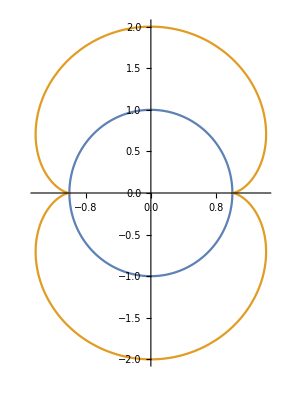
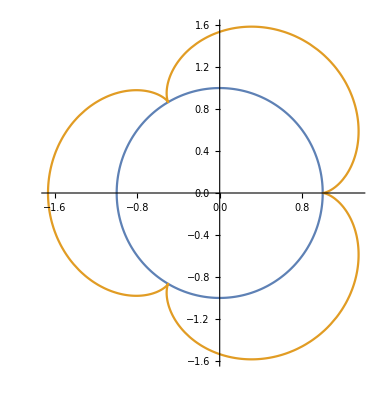
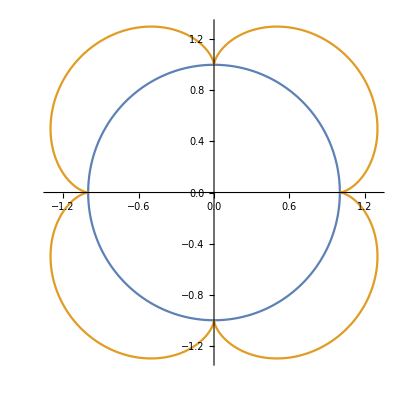
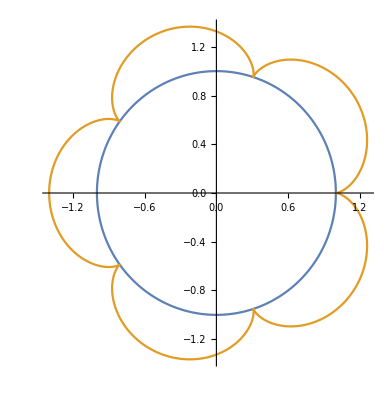
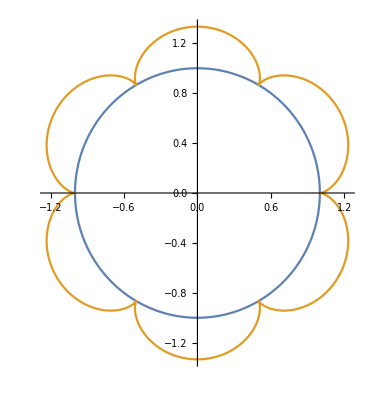
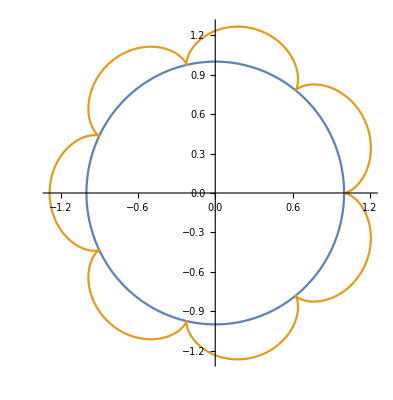

```mathematica
Table[
Show[
ParametricPlot[{
{R Cos[t],R Sin[t]},

{Cos[t](R+r-r Cos[(R t)/r])+r Sin[t]Sin[(R t)/r],Sin[t](R+r-r Cos[(R t)/r])-r Cos[t]Sin[(R t)/r]}
},{t,0,2π}]],{R,1},{r,{1,1/2,1/3,1/4,1/5,1/6,1/7}}]
```

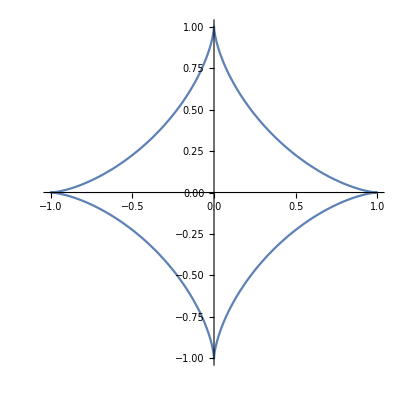

```mathematica
ParametricPlot[{Cos[t]^3, Sin[t]^3},{t,0,2π}]
```

```mathematica
Show[
ParametricPlot3D[{Cos[φ]Cos[θ],Sin[φ]Cos[θ],Sin[θ]},{φ,0,2π},{θ,-π/2,π/2},Boxed->False,Axes->False,PlotStyle->{RGBColor[0.23,0.64,0.53,0.45]},Mesh->None],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,+√3 Abs[Cos[t]]Abs[Sin[t]]},{t,0,2π},PlotStyle->{Red}],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,-√3 Abs[Cos[t]]Abs[Sin[t]]},{t,0,2π},PlotStyle->{Blue}],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,0},{t,0,2π},PlotStyle->Black]
]
```

-Graphics3D-

```mathematica
Manipulate[
Show[
ParametricPlot3D[{Cos[φ]Cos[θ],Sin[φ]Cos[θ],c Sin[θ]},{φ,0,2π},{θ,-π/2,π/2},Boxed->False,Axes->False,PlotStyle->{RGBColor[0.23,0.64,0.53,0.45]},Mesh->None],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,+c √3 Abs[Cos[t]]Abs[Sin[t]]},{t,0,2π},PlotStyle->{Red}],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,-c √3 Abs[Cos[t]]Abs[Sin[t]]},{t,0,2π},PlotStyle->{Blue}],
ParametricPlot3D[{Cos[t]^3,Sin[t]^3,0},{t,0,2π},PlotStyle->Black]
],{c,0.1,3}
]
```

```mathematica
Manipulate[
ParametricPlot3D[
{{u,v,√(c(u^2+v^2)-t)},{u,v,-√(c(u^2+v^2)-t)}},
{u,-3,3},
{v,-3,3},
Boxed->False,
Axes->True,
PlotRange->{{-3,3},{-3,3}},
PlotPoints->100
],{c,1,6},{t,-2,2}
]
```

```mathematica
{N[ArcTan[3/2]],N[ArcCos[2/(√13)]]}
```

{0.982794,0.982794}

```mathematica
Manipulate[
Show[
ContourPlot[x^2+y^2==1,{x,-3,3},{y,-3,3}],
ParametricPlot[{a+t(1-a^2),b+t(-a b+√(a^2+b^2-1))},{t,-3,3}],
ParametricPlot[{a+t(1-a^2),b+t(-a b-√(a^2+b^2-1))},{t,-3,3}],
Graphics[{Point[{a,b}]}]
],{a,-2,2},{b,-2,2}
]
```

```mathematica
Manipulate[
Show[
ContourPlot[x^2/a^2+y^2/b^2==1,{x,-a-1,a+1},{y,-b-1,b+1},AspectRatio->Automatic],
ContourPlot[(x a Cos[x0])/a^2+(y b Sin[x0])/b^2==1,{x,-a-1,a+1},{y,-b-1,b+1}]
],{a,1,3},{b,1,3},{x0,0,2π}
]
```

```mathematica
Manipulate[
Show[
ParametricPlot[{x,Tan[ρ/2]x},{x,-3,3},Axes->True,PlotRange->{{-3,3},{-3,3}}],
Graphics[{PointSize[Large],Blue,Point[{{{Cos[ρ],Sin[ρ]},{Sin[ρ],-Cos[ρ]}}.{x,y}}],Black,Point[{x,y}]}]

],{ρ,0,π},{{x,1},-3,3},{{y,1},-3,3}
]
```

```mathematica
Manipulate[
Show[
Graphics[{PointSize[Large],Blue,Point[{{{Cos[φ],Sin[φ]},{Sin[φ],-Cos[φ]}}.{x,y}}],Black,Point[{x,y}]},Axes->True,PlotRange->{{-3,3},{-3,3}}]

],{φ,0,2π},{{x,1},-3,3},{{y,1},-3,3}
]
```

```mathematica
α[t_]:={Exp[t]Cos[t],Exp[t]Sin[t],t};
```

```mathematica
FullSimplify[((D[α[u],u]×D[α[u],{u,2}])×D[α[u],u])/Norm[(D[α[u],u]×D[α[u],{u,2}])×D[α[u],u]],Element[u,Reals]]
```

{(-Sin[u]-ⅇ^(2 u) (Cos[u]+Sin[u]))/(√(1+3 ⅇ^(2 u)+2 ⅇ^(4 u))),(Cos[u]+ⅇ^(2 u) (Cos[u]-Sin[u]))/(√(1+3 ⅇ^(2 u)+2 ⅇ^(4 u))),-ⅇ^u/(√(1+3 ⅇ^(2 u)+2 ⅇ^(4 u)))}

```mathematica
o--------------------------------------iio--------------------------------iiiiiiiiiiiiiiiiiiiiiii-iiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiiixc+
```

```mathematica
FullSimplify[((D[α[t],t]×D[α[t],{t,2}])×D[α[t],t])/Norm[(D[α[t],t]×D[α[t],{t,2}])×D[α[t],t]],Element[t,Reals]]
```

{(-Sin[t]-ⅇ^(2 t) (Cos[t]+Sin[t]))/(√(1+3 ⅇ^(2 t)+2 ⅇ^(4 t))),(Cos[t]+ⅇ^(2 t) (Cos[t]-Sin[t]))/(√(1+3 ⅇ^(2 t)+2 ⅇ^(4 t))),-ⅇ^t/(√(1+3 ⅇ^(2 t)+2 ⅇ^(4 t)))}

```mathematica
FullSimplify[((R^2+1)/R^3(R2-R1^2/(R^3+R))R)/(R1^2(1+1/R^2)+(R^2+1)/R(R2-R1^2/(R^3+R))),R>0]
```

(-R1^2+R (1+R^2) R2)/(R^2 (R2+R (R1^2+R R2)))

```mathematica
povrs[u_,v_]:={u,v,3 u^2 v-v^3};
a[u_,v_]:=(D[povrs[x,v],x]/.x->u)×(D[povrs[u,x],x]/.x->v)
n[u_,v_]:=a[u,v]/(√(a[u,v].a[u,v]))
FullSimplify[n[ξ t,η t]]
```

{-(6 t^2 η ξ)/(√(1+9 t^4 (η^2+ξ^2)^2)),(3 t^2 (η-ξ) (η+ξ))/(√(1+9 t^4 (η^2+ξ^2)^2)),1/(√(1+9 t^4 (η^2+ξ^2)^2))}